```mathematica
Clear["Global`*"];
GenerateCoordinates[range_, amount_]:=(
x=RandomSample[Range[range],amount];
y=RandomSample[Range[range],amount];
towers = {x,y};
Return[towers];
);
```

```mathematica
powerTowers = GenerateCoordinates[100,10]
```

{{15,76,69,1,55,78,2,23,5,52},{1,70,57,40,20,80,50,4,91,68}}

```mathematica
GetPower[i_,j_,towers_]:=(
MaxPower = 0;
For[k=1,k≤10, k++,
CalculatedPower = 0;
StationStaticPower=0;
If[k≤5, StationStaticPower = 100, 
If[k≤8, StationStaticPower= 200, StationStaticPower = 300]
];
StationPowerX=towers[[1,k]];
StationPowerY=towers[[2,k]];
DxD=((i-StationPowerX)^2 + (j-StationPowerY)^2);
If[DxD ==0, CalculatedPower = StationStaticPower, CalculatedPower=StationStaticPower / DxD];
If[CalculatedPower > MaxPower, MaxPower = CalculatedPower,];
];
Return[MaxPower];
);
```

```mathematica
N[GetPower[17,80, powerTowers]]
```

11.1111

```mathematica
MatrixPlot[Rescale[Table[GetPower[x,y,powerTowers],{x,100},{y,100}]],ColorFunction->Hue];
```

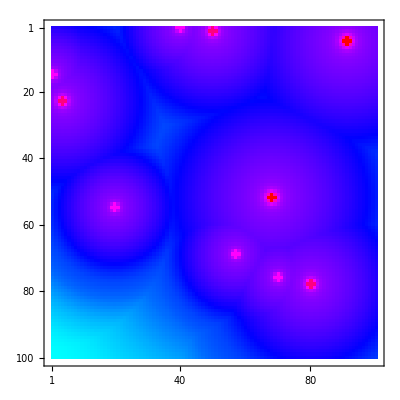

```mathematica
%151
```

```mathematica
Plot3D[GetPower[x,y, powerTowers],{x,1,100},{y,1,100},ColorFunction->Hue];
```

```mathematica
%153
```

-Graphics3D-

```mathematica
ListPlot3D[Rescale[Table[GetPower[y,x,powerTowers],{x,100},{y,100}]],InterpolationOrder->0,ColorFunction->Hue,Mesh->None,Filling->Axis]
```

-Graphics3D-

```mathematica
populationDensity=Table[RandomInteger[{100,10000}],{i,100},{j,100}];
powerMapTable = Table[N[GetPower[x,y,powerTowers]],{x,100},{y,100}];
populationDensity[[1,1]]
```

9108

```mathematica
allpopulation =Sum[populationDensity[[i,j]],{i,1,100}, {j,1,100}];
```

```mathematica
50908540
```

50908540

```mathematica
populationGoodCoverage =Sum[If[powerMapTable[[i,j]]>1,populationDensity[[i,j]],0],{i,1,100}, {j,1,100}];
```

```mathematica
20687928
```

20687928

```mathematica
N[populationGoodCoverage/allpopulation]
```

0.342487